-Graphics-
-Graphics-

Block 13-point

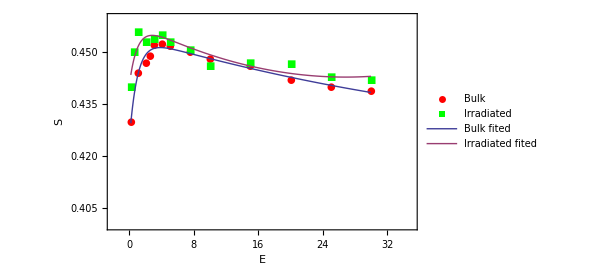

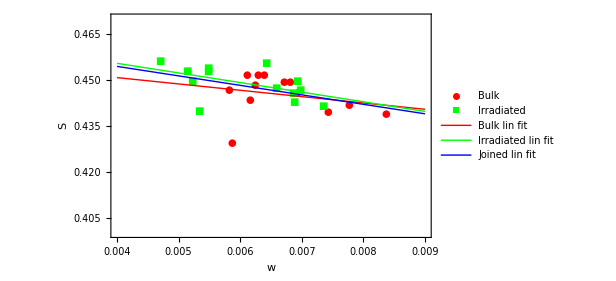

Average S(w) bulk=  {0.00667985 ;  0.445154};

Average S(w) irr=  {0.00609915 ;  0.448762};

S(w) irr - S(w) bulk ::  {-0.000580692 ;  0.00360761};

```mathematica
b={{0.2,0.43},{1,0.444},{2,0.447},{2.5,0.449},{3,0.452},{4,0.4525},{5,0.4519},{7.5,0.45},{10,0.44801},{15,0.446},{20,0.442},{25,0.4400},{30,0.439}};
irr={{0.2,0.44},{0.5,0.45},{1,0.456},{2,0.453},{3,0.454},{4,0.455},{5,0.453},{7.5,0.4508},{10,0.446},{15,0.447},{20,0.4468},{25,0.4430},{30,0.442}};
fb=Fit[b,{1,x,x^2, Exp[-x]},x];
firr=Fit[irr,{1,x,x^2,Exp[-x]},x];
Show[ListPlot[{b,irr},PlotStyle->{Red,Green},PlotRange->{{-2,35},{0.4,0.46}},PlotMarkers->{Automatic,10},LabelStyle->Directive[Black,FontSize->20,FontFamily->"Helvetica"],AxesStyle->Black,FrameLabel->{"E","S"},Frame->True,PlotLegends->{"Bulk","Irradiated"}],Plot[{fb,firr},{x,0.18,30},PlotLegends->{"Bulk fited","Irradiated fited"}]]
SWi={{0.0047,0.4561},{0.00514,0.453},{0.00522,0.4497},{0.005323,0.4397},{0.00547,0.4539000},{0.005473,0.4529},{0.006418,0.455300},{0.006582,0.447300},{0.006861,0.445800},{0.006867,0.442700},{0.006926,0.4495},{0.006967,0.4465},{0.007342,0.441500}};
SWb={{0.005811,0.446600},{0.005869,0.429400},{0.00611,0.4514},{0.00616,0.4435},{0.006239,0.44830},{0.006286,0.4517},{0.00638,0.4515},{0.006708,0.449200},{0.006802,0.449400},{0.006926,0.445800},{0.007416,0.4396011},{0.007771,0.441700},{0.00836,0.4389}};
ListPlot[{SWb,SWi},PlotStyle->{Red,Green},PlotRange->{{0.004,0.009},{0.4,0.47}},PlotMarkers->{Automatic,10},LabelStyle->Directive[Black,FontSize->20,FontFamily->"Helvetica"],AxesStyle->Black,Frame->True,PlotLegends->{"Bulk","Irradiated"}];
fbi=Fit[SWb,{1,x},x];
firri=Fit[SWi,{1,x},x];
fa=Fit[Sort[Join[SWb,SWi],#1[[1]]<#2[[1]]&],{1,x},x];
Show[ListPlot[{SWb,SWi},PlotStyle->{Red,Green},PlotRange->{{0.004,0.009},{0.4,0.47}},PlotMarkers->{Automatic,10},LabelStyle->Directive[Black,FontSize->20,FontFamily->"Helvetica"],AxesStyle->Black,FrameLabel->{"w","S"},Frame->True,PlotLegends->{"Bulk","Irradiated"}],Plot[{fbi,firri,fa},{x,0.004,0.009},PlotStyle->{Red,Green,Blue},PlotLegends->{"Bulk lin fit","Irradiated lin fit","Joined lin fit"}]]
Print[StringJoin["Average S(w) bulk=  {",ToString[(Mean[SWb][[1]])]," ;  ", ToString[(Mean[SWb][[2]])],"};"]]
Print[StringJoin["Average S(w) irr=  {",ToString[(Mean[SWi][[1]])]," ;  ", ToString[(Mean[SWi][[2]])],"};"]]
Print[StringJoin["S(w) irr - S(w) bulk ::  {",ToString[((Mean[SWi]-Mean[SWb])[[1]])]," ;  ", ToString[((Mean[SWi]-Mean[SWb])[[2]])],"};"]]
```

Block 12- point

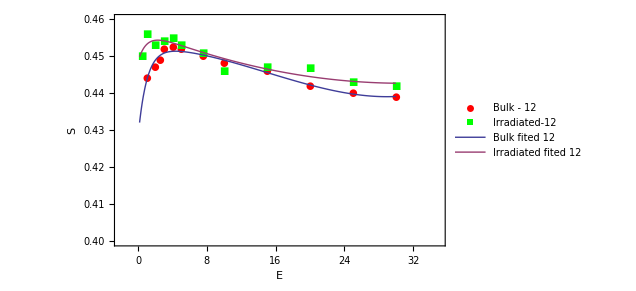

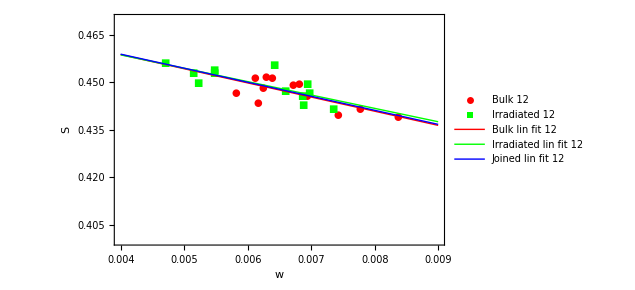

```mathematica
bm={{1,0.444},{2,0.447},{2.5,0.449},{3,0.452},{4,0.4525},{5,0.4519},{7.5,0.45},{10,0.44801},{15,0.446},{20,0.442},{25,0.4400},{30,0.439}};
irrm={{0.5,0.45},{1,0.456},{2,0.453},{3,0.454},{4,0.455},{5,0.453},{7.5,0.4508},{10,0.446},{15,0.447},{20,0.4468},{25,0.4430},{30,0.442}};
fbm=Fit[bm,{1,x,x^2,x^3, Exp[-x]},x];
firrm=Fit[irrm,{1,x,x^2,Exp[-x]},x];
Show[ListPlot[{bm,irrm},PlotStyle->{Red,Green},PlotRange->{{-2,35},{0.4,0.46}},PlotMarkers->{Automatic,10},LabelStyle->Directive[Black,FontSize->20,FontFamily->"Helvetica"],AxesStyle->Black,FrameLabel->{"E","S"},Frame->True,PlotLegends->{"Bulk - 12","Irradiated-12"}],Plot[{fbm,firrm},{x,0.18,30},PlotLegends->{"Bulk fited 12","Irradiated fited 12"}]]
SWim={{0.0047,0.4561},{0.00514,0.453},{0.00522,0.4497},{0.00547,0.4539000},{0.005473,0.4529},{0.006418,0.455300},{0.006582,0.447300},{0.006861,0.445800},{0.006867,0.442700},{0.006926,0.4495},{0.006967,0.4465},{0.007342,0.441500}};
SWbm={{0.005811,0.446600},{0.00611,0.4514},{0.00616,0.4435},{0.006239,0.44830},{0.006286,0.4517},{0.00638,0.4515},{0.006708,0.449200},{0.006802,0.449400},{0.006926,0.445800},{0.007416,0.4396011},{0.007771,0.441700},{0.00836,0.4389}};
ListPlot[{SWbm,SWim},PlotStyle->{Red,Green},PlotRange->{{0.004,0.009},{0.4,0.47}},PlotMarkers->{Automatic,10},LabelStyle->Directive[Black,FontSize->20,FontFamily->"Helvetica"],AxesStyle->Black,FrameLabel->{"w","S"},Frame->True,PlotLegends->{"Bulk 12","Irradiated 12"}];
fbim=Fit[SWbm,{1,x},x];
firrim=Fit[SWim,{1,x},x];
fam=Fit[Sort[Join[SWbm,SWim],#1[[1]]<#2[[1]]&],{1,x},x];
Show[ListPlot[{SWbm,SWim},PlotStyle->{Red,Green},PlotRange->{{0.004,0.009},{0.4,0.47}},PlotMarkers->{Automatic,10},LabelStyle->Directive[Black,FontSize->20,FontFamily->"Helvetica"],AxesStyle->Black,FrameLabel->{"w","S"},Frame->True,PlotLegends->{"Bulk 12","Irradiated 12"}],Plot[{fbim,firrim,fam},{x,0.004,0.009},PlotStyle->{Red,Green,Blue},PlotLegends->{"Bulk lin fit 12","Irradiated lin fit 12","Joined lin fit 12"}]]
```